```mathematica
(* Задача 1 *)
(* Must include brackets or Mathematica does not parse *)
∫_0^(Pi/2) (-8 Cos[ϕ]^2 Sin[ϕ]+8 Sin[ϕ]^2 Cos[ϕ])ⅆϕ + ∫_0^1 (24 t^2+t^2)ⅆt
∫_0^Pi -4t Sin[t]Cos[t] √(4 Cos[t]^2+1+4 Sin[t]^2)ⅆt
```

25/3

√5 π

```mathematica
(* Задача 2 *)
∫_0^(2Pi) √((1-Cos[t])^2+Sin[t]^2)ⅆt
```

8

```mathematica
(* Задача 4 *)
(* The substance may leave Ω only from the boundry ∂Ω *) 
(* If j is the flow then j.n is the amount leaving at some point of ∂Ω *) 
r[t_]:={Cos[t],Sin[t]};
n[t_]:=Normalize[r[t]]
j[t_]:={2 Cos[t]+Sin[t],Cos[t]};
(* Using Abs to get flow regardless of considering "going inside" or "going outside" *)
Abs[Integrate[j[t].n[t],{t,0,2Pi}]]
(* This one calculates "overall flow", rather than the resulting difference "gaining" and "losing" substance 
  Is there any useful physical meaning?*)
Integrate[Abs[j[t].n[t]],{t,0,2Pi}]
```

2 π

4+π

True

16

16

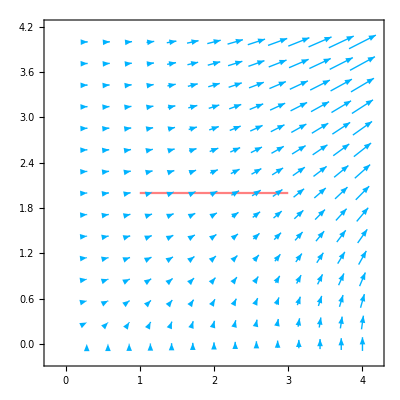

```mathematica
(* Задача 5 *)
Field[x_,y_]:={2x y,x^2}
PotentialF[x_,y_]:=x^2 y
(*The field is conservative*)
∇_{x,y} PotentialF[x,y] == Field[x,y]
(*Since the path does not matter we can compute the integral on a straight line*)
Integrate[4(1+t),{t,0,2}]
(*Which is the same as applying Newton-Leibniz*)
PotentialF[3,2]-PotentialF[1,2]

Show[{
VectorPlot[Field[x,y],{x,0,4},{y,0,4},VectorStyle->Blend[{Blue,Cyan},0.7]],
Plot[2,{x,1,3},PlotStyle->Pink]
}]
```